```mathematica
a=2Pi/5;
r0={1,0,0};
r1={Cos[a],Sin[a],0};
r2={Cos[2a],Sin[2a],0};
r3={Cos[3a],Sin[3a],0};
r4={Cos[4a],Sin[4a],0};
```

```mathematica
starvectors={r0,r1,r2,r3,r4};
basis =Graphics[Arrow[{{0,0},#}]&/@starvectors[[All,{1,2}]],Axes->True];
```

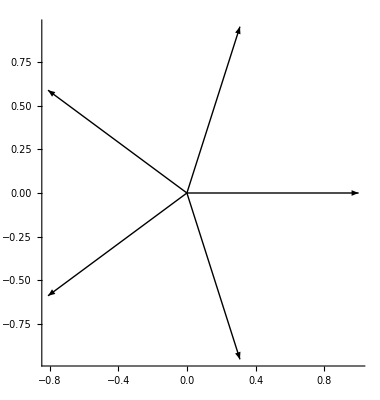

```mathematica
Show[basis]
```

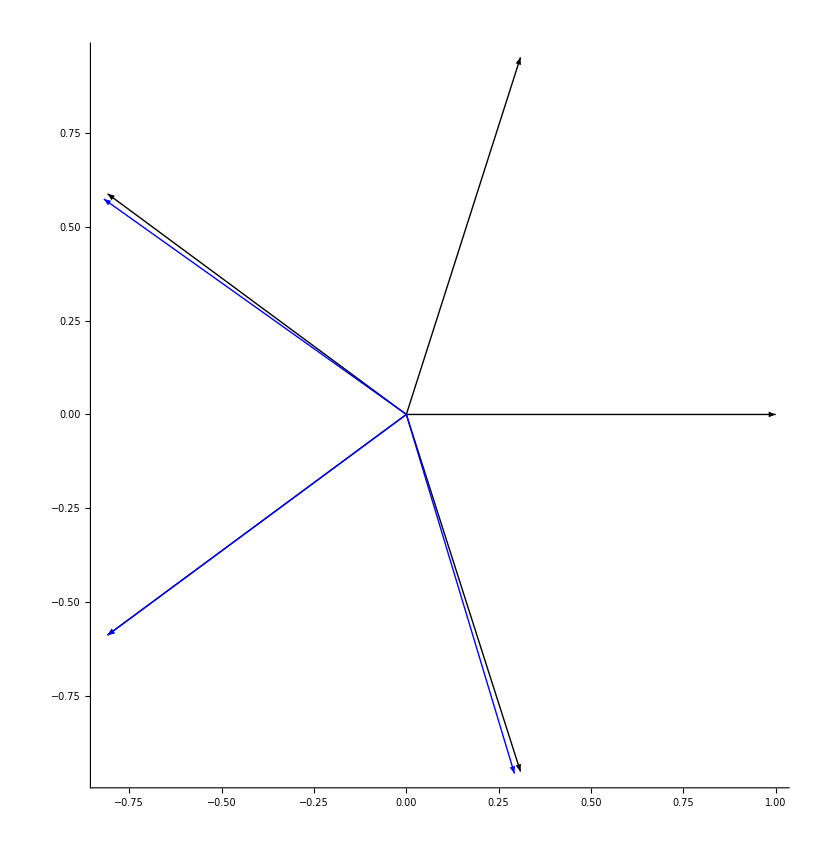

```mathematica
tau=8/5;
A=tau-1;
Nr4=Normalize[-r1+A r0];
Nr2=Normalize[ A r1 - r0];
Nr3=Normalize[-100(r0+r1)];
newvectors={Nr2,Nr4,Nr3};
Nbasis =Graphics[{Blue,Arrow[{{0,0},#}]&/@newvectors[[All,{1,2}]],Axes->True}];
Show[basis,Nbasis]
```